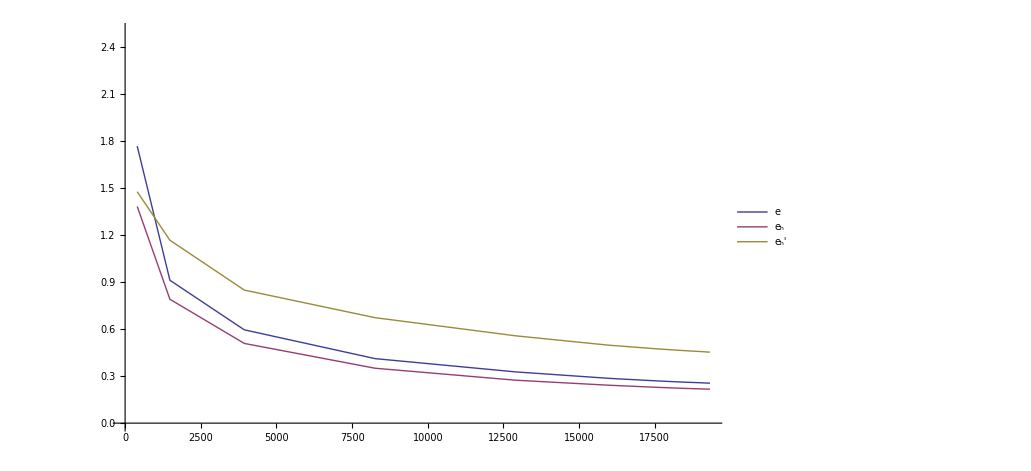

```mathematica
SetDirectory["d:\\Learn\\Diploma\\DiplomaText\\include\\8NumResults\\problem1\\my\\errors\\"];
triangles = Import["triangles.txt","List"];
realErr = Import["realError.txt","List"];
myErr = Import["myError.txt","List"];
ostErr = Import["ostError.txt","List"];

ListLinePlot[{
	Transpose[{triangles, realErr}],
	Transpose[{triangles, myErr}],
	Transpose[{triangles, ostErr}]
},
PlotLegends->Placed[{
ToExpression["e",TeXForm,HoldForm],
ToExpression["e_h",TeXForm,HoldForm],
ToExpression["e_h^\prime",TeXForm,HoldForm]
},{0.8,.5}],
Filling->xis,
PlotRange -> {0,2.5}
]
```

```mathematica
SetDirectory["d:\\Learn\\Diploma\\DiplomaText\\include\\8NumResults\\problem1\\ost\\errors\\"];
triangles = Import["triangles.txt","List"];
realErr = Import["realError.txt","List"];
myErr = Import["myError.txt","List"];
ostErr = Import["ostError.txt","List"];

ListLinePlot[{
	Transpose[{triangles, realErr}],
	Transpose[{triangles, myErr}],
	Transpose[{triangles, ostErr}]
},
PlotLegends->Placed[{
ToExpression["e",TeXForm,HoldForm],
ToExpression["e_h",TeXForm,HoldForm],
ToExpression["e_h^\prime",TeXForm,HoldForm]
},{0.8,.5}],
FontSize->14,
Filling->xis,
PlotRange -> {0,2.5}]
```

ListLinePlot::optx: Unknown option LegendSize → {3, 3} in ListLinePlot[« 1 »].

ListLinePlot[{{{400,1.76786},{1320,1.17211},{4040,0.759131},{10576,0.553194},{21198,0.442613},{30261,0.376981},{35951,0.351502},{39328,0.339216},{41218,0.334398},{42237,0.332017},{42756,0.330869},{43034,0.330396},{43198,0.329806},{43293,0.329611},{43355,0.329003},{43377,0.328993},{43387,0.328989},{43393,0.328986},{43397,0.328986},{43399,0.328977}},{{400,1.38269},{1320,1.09015},{4040,0.729557},{10576,0.52786},{21198,0.436183},{30261,0.373815},{35951,0.349541},{39328,0.336209},{41218,0.332071},{42237,0.329619},{42756,0.328726},{43034,0.32833},{43198,0.327479},{43293,0.327282},{43355,0.326297},{43377,0.326289},{43387,0.326287},{43393,0.326286},{43397,0.326285},{43399,0.32628}},{{400,1.47688},{1320,1.16271},{4040,0.721559},{10576,0.448572},{21198,0.315549},{30261,0.265592},{35951,0.244297},{39328,0.233749},{41218,0.228304},{42237,0.22551},{42756,0.224138},{43034,0.223383},{43198,0.222957},{43293,0.222705},{43355,0.222556},{43377,0.222499},{43387,0.222475},{43393,0.222458},{43397,0.222447},{43399,0.222443}}},PlotLegends→Placed[{e,e_h,e_h'},{0.8,0.5}],LegendSize→{3,3},Filling→xis,PlotRange→{0,2.5}]